# Prices visualization

## Initialization

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory@NotebookDirectory[],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

```mathematica
ExportImages[file_,frames_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[Length[frames]]];
directory = DirectoryName[file];
name = FileBaseName[file];

MapIndexed[
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[#2,10,indexLength],".png"]}],
#1
]&,
frames
]
];
```

```mathematica
FillMissing[prices_]:=Block[{propagateBackwards,propagateForward},
propagateBackwards = FixedPoint[
SequenceReplace[#,
{
{"null",x_ /;NumberQ[x]}:>Sequence[x,x],
{None,x_ /;NumberQ[x]}:>Sequence[x,x]
}
]&,
prices
];
propagateForward = FixedPoint[
SequenceReplace[#,
{
{x_ /;NumberQ[x],"null"}:>Sequence[x,x],
{x_ /;NumberQ[x],None}:>Sequence[x,x],
{x_ /;NumberQ[x],""}:>Sequence[x,x]
}
]&,
propagateBackwards
];
Return[propagateForward];
];

ToFinancialData[dataset_]:=Block[{formatted},
formatted = Map[{DateList[First[#]],Rest[#]}&,dataset];
DeleteCases[formatted,{_,{"","","","",""}}]
];
ImportDatabase[date_]:=Block[{files,stocks,dataset},
files = FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV",date}]];
stocks = Map[FileBaseName,files];

Association@Map[FileBaseName[#]->ToFinancialData@Drop[Import[#],1]&,files]
];
```

```mathematica
dateFolders = Select[FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV"}]],FileExtension[#]==""&];
```

```mathematica
dates = Map[FileBaseName,dateFolders]
```

{20-01-2020,21-01-2020,22-01-2020,23-01-2020}

```mathematica
database =ImportDatabase[Last[dates]];
```

```mathematica
database // Keys
```

{AC.MX,ALPEKA.MX,ALSEA.MX,AMXL.MX,ASURB.MX,BBAJIOO.MX,BIMBOA.MX,BOLSAA.MX,BSMXB.MX,CEMEXCPO.MX,CUERVO.MX,GAPB.MX,GCARSOA1.MX,GCC.MX,GENTERA.MX,GFNORTEO.MX,GMEXICOB.MX,GRUMAB.MX,IENOVA.MX,KIMBERA.MX,KOFUBL.MX,LABB.MX,LIVEPOLC-1.MX,MEGACPO.MX,OMAB.MX,ORBIA.MX,PE&OLES.MX,PINFRA.MX,RA.MX,TLEVISACPO.MX}

```mathematica
plots = Table[
TradingChart[database[key],
ChartElementFunction->"Candlestick",
PlotLabel->key,
ImageSize->300,
PerformanceGoal->"Speed"
],
{key,Keys[database]}
];
```

```mathematica
Length[plots]
```

30

```mathematica
InteractiveTradingChart[
database["TLEVISACPO.MX"],
ChartElementFunction->"Candlestick",
PlotLabel->"TLEVISACPO.MX",
ImageSize->800
]
```

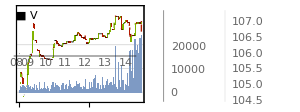
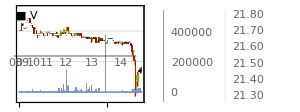
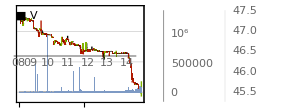
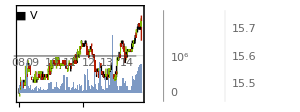
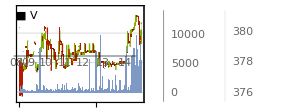
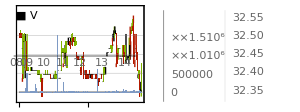
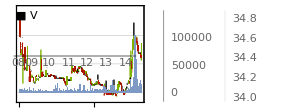
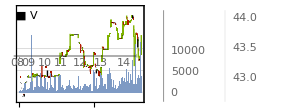
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid@Partition[plots,5]
```